```mathematica
datos = Import[FileNameJoin[{NotebookDirectory[],"numbers.dat"}]];
```

```mathematica
numeros = First[Transpose[datos]];
```

```mathematica
sinCeros = DeleteCases[numeros,0.0|"nan"|"-nan"];
```

```mathematica
{intervalos,freq} = HistogramList[sinCeros];
```

```mathematica
normalizados = Quiet@N[intervalos/(1.79769*10^308)];
```

```mathematica
histograma = Transpose[{Drop[normalizados,1],freq}];
```

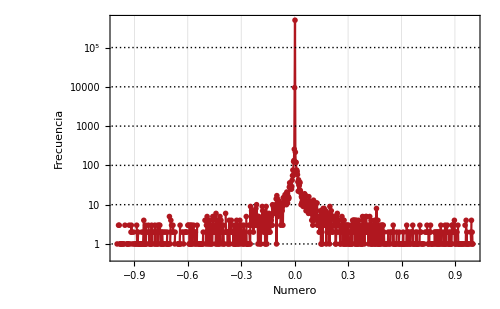

```mathematica
ListLinePlot[histograma,
PlotRange->All,
ScalingFunctions->"Log",
PlotTheme->"Monochrome",
FrameLabel->{Style["Numero",15], Style["Frecuencia",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
Frame->True,
ImageSize->500,
GridLines->Automatic
]
```

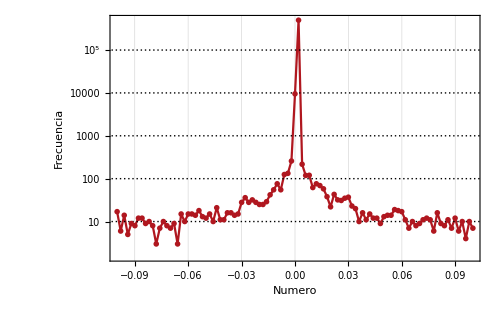

```mathematica
ListLinePlot[
Select[histograma,-0.1<First[#]<0.1&],
PlotRange->All,
ScalingFunctions->"Log",
PlotTheme->"Monochrome",
FrameLabel->{Style["Numero",15], Style["Frecuencia",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
Frame->True,
ImageSize->500,
GridLines->Automatic
]
```